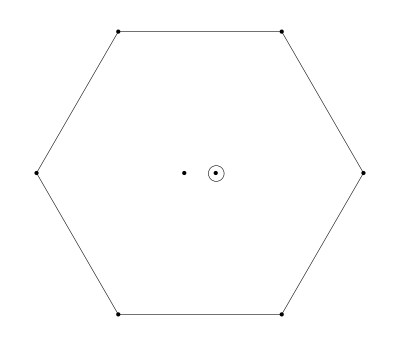

Y=0,  I_3=0

(ud-du)(d̄ū-ūd̄)+2(ds-sd)(d̄s̄-s̄d̄)+(us-su)(s̄ū-ūs̄)

```mathematica
(*-------------------------------*)
```

The current J:

2 (d_a^T C σ^αμ s_b-s_a^T C σ^αμ d_b) ((d̄)_a σ^αμ C((s̄)_b)^T)+2 (d_a^T C σ^αμ s_b-s_a^T C σ^αμ d_b) ((d̄)_b σ^αμ C((s̄)_a)^T)+2 (s_a^T C σ^αμ d_b-d_a^T C σ^αμ s_b) ((s̄)_a σ^αμ C((d̄)_b)^T)+2 (s_a^T C σ^αμ d_b-d_a^T C σ^αμ s_b) ((s̄)_b σ^αμ C((d̄)_a)^T)+(u_a^T C σ^αμ d_b) ((d̄)_a σ^αμ C((ū)_b)^T-(ū)_a σ^αμ C((d̄)_b)^T)+(d_a^T C σ^αμ u_b) ((ū)_a σ^αμ C((d̄)_b)^T-(d̄)_a σ^αμ C((ū)_b)^T)+(u_a^T C σ^αμ d_b) ((d̄)_b σ^αμ C((ū)_a)^T-(ū)_b σ^αμ C((d̄)_a)^T)+(d_a^T C σ^αμ u_b) ((ū)_b σ^αμ C((d̄)_a)^T-(d̄)_b σ^αμ C((ū)_a)^T)+(u_a^T C σ^αμ s_b) ((s̄)_a σ^αμ C((ū)_b)^T-(ū)_a σ^αμ C((s̄)_b)^T)+(s_a^T C σ^αμ u_b) ((ū)_a σ^αμ C((s̄)_b)^T-(s̄)_a σ^αμ C((ū)_b)^T)+(u_a^T C σ^αμ s_b) ((s̄)_b σ^αμ C((ū)_a)^T-(ū)_b σ^αμ C((s̄)_a)^T)+(s_a^T C σ^αμ u_b) ((ū)_b σ^αμ C((s̄)_a)^T-(s̄)_b σ^αμ C((ū)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-24 (d̄(γ̄)^5 s s̄(γ̄)^5 d)+4 (d̄ σ^μν d s̄ σ^μν s)-4 (d̄ σ^μν s s̄ σ^μν d)+12 (d̄(γ̄)^5 d) (2 (s̄(γ̄)^5 s)-ū(γ̄)^5 u)+12 (d̄ 1d) (2 (s̄ 1s)-ū 1u)-24 (d̄ 1s s̄ 1d)+12 (d̄(γ̄)^5 u ū(γ̄)^5 d)-2 (d̄ σ^μν d ū σ^μν u)+2 (d̄ σ^μν u ū σ^μν d)+12 (d̄ 1u ū 1d)-12 (s̄(γ̄)^5 s ū(γ̄)^5 u)+12 (s̄(γ̄)^5 u ū(γ̄)^5 s)-2 (s̄ σ^μν s ū σ^μν u)+2 (s̄ σ^μν u ū σ^μν s)-12 (s̄ 1s ū 1u)+12 (s̄ 1u ū 1s)
```

Π(q^2)=
-(3 log(-q^2/μ^2) q^8)/(40 π^6)-(11 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(2 π^5)-(20 ⟨ d̄ d⟩ log(-q^2/μ^2) m_d q^4)/π^4-(20 ⟨ s̄ s⟩ log(-q^2/μ^2) m_s q^4)/π^4-(8 ⟨ ū u⟩ log(-q^2/μ^2) m_u q^4)/π^4-(480 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/π^2-(480 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/π^2-(192 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/π^2+(6 ⟨G^3⟩ log(-q^2/μ^2) q^2)/π^6-(192 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/π^2+(384 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(384 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2-(730 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(9 π^2)-(146 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(9 π^2)+(292 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(9 π^2)-(146 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(9 π^2)-(730 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(9 π^2)+(292 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(9 π^2)+(292 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)+(292 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)-(292 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(9 π^2)-(160 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(π q^2)-(160 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(π q^2)-(64 ⟨ GG ⟩ ⟨ ū u⟩^2)/(π q^2)-(5 ⟨ d̄ Gd⟩^2)/(6 π^2 q^2)-(5 ⟨ s̄ Gs⟩^2)/(6 π^2 q^2)-⟨ ū Gu⟩^2/(3 π^2 q^2)-(64 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(π q^2)+(128 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(π q^2)+(128 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(π q^2)-(⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(3 π^2 q^2)+(2 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)+(2 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)-(7168 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 m_d)/(3 q^2)-(1792 ⟨ d̄ d⟩ ⟨ ū u⟩^2 m_d)/(3 q^2)-(1792 ⟨ s̄ s⟩ ⟨ ū u⟩^2 m_s)/(3 q^2)-(7168 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ m_s)/(3 q^2)+(1536 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (2 m_d+2 m_s-m_u))/q^2-(1792 ⟨ d̄ d⟩^2 ⟨ ū u⟩ m_u)/(3 q^2)-(1792 ⟨ s̄ s⟩^2 ⟨ ū u⟩ m_u)/(3 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

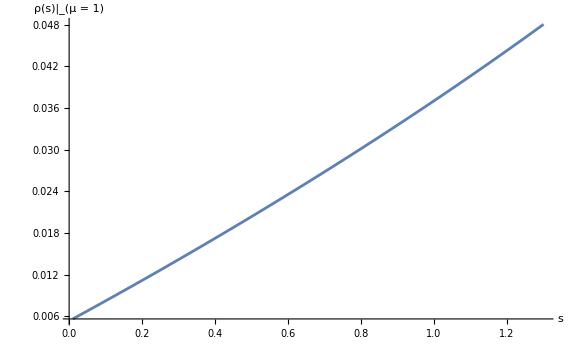
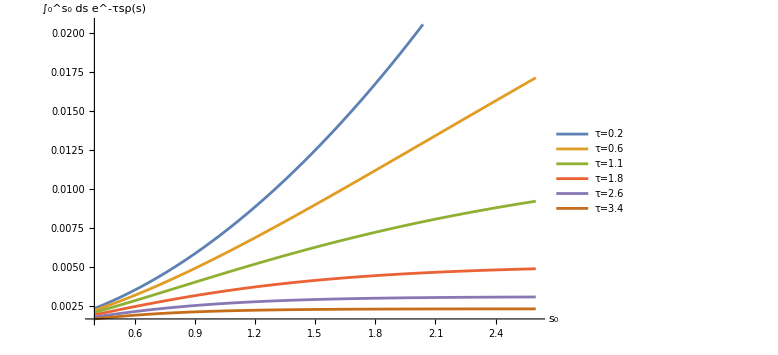

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

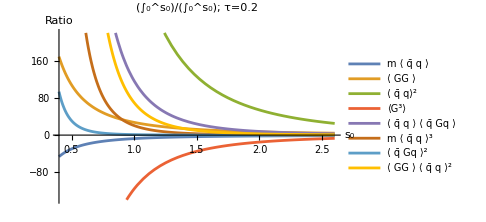
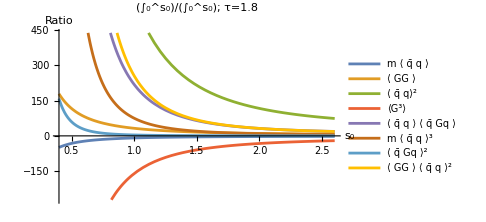
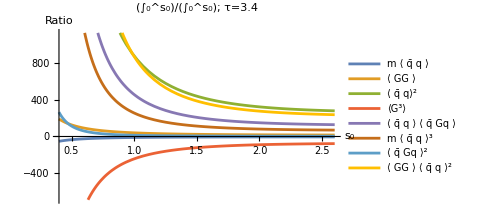

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

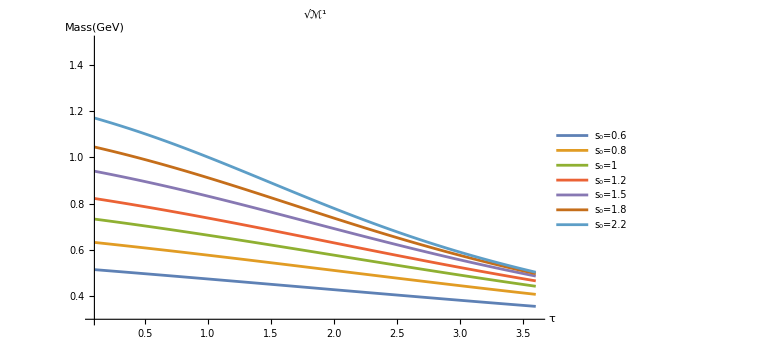
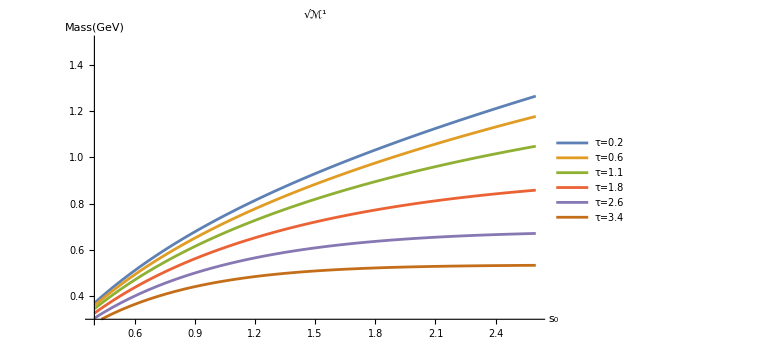

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

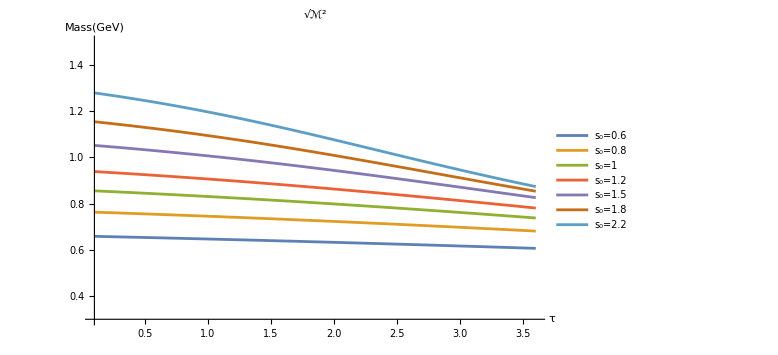
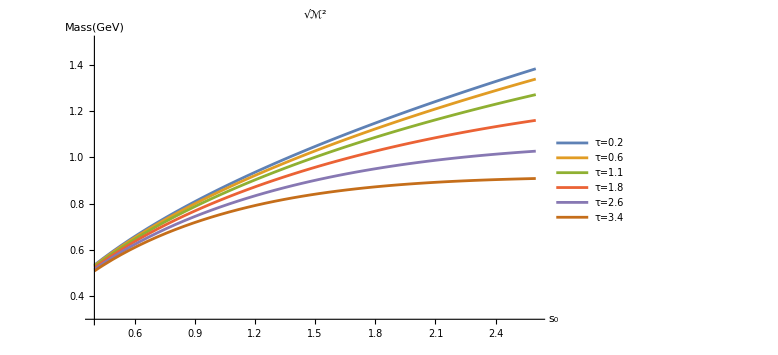

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

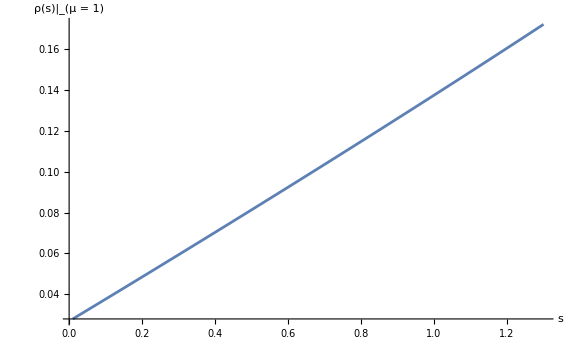
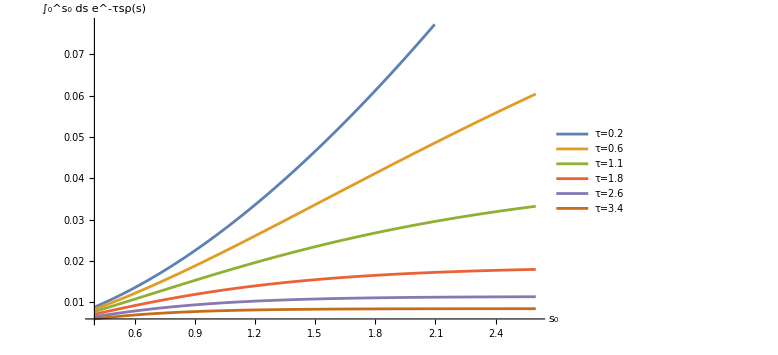

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

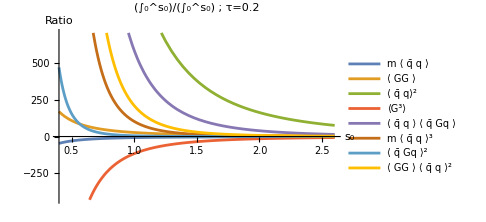
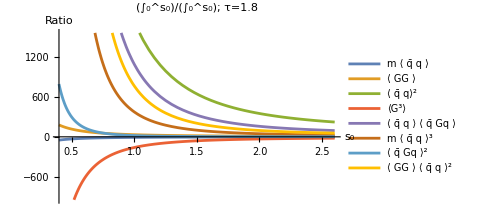
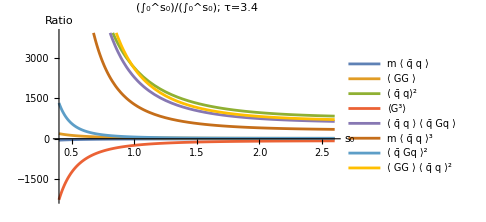

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

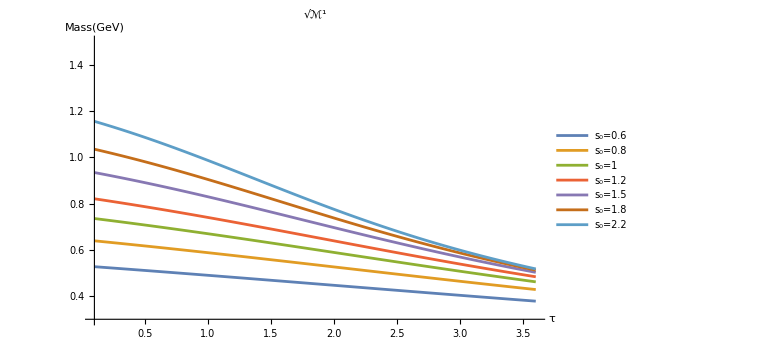
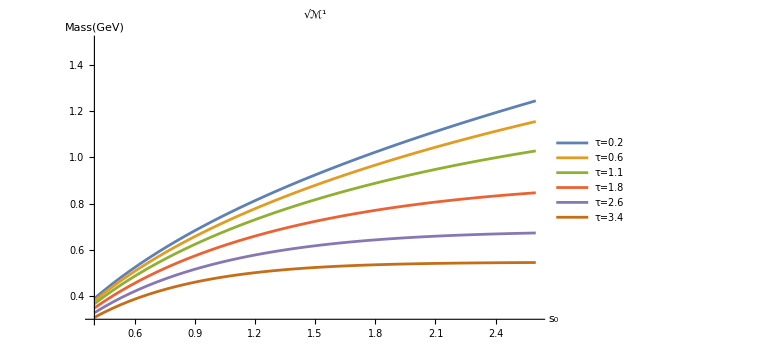

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5